# NNListLinePlotMean Tests

```mathematica
<<NounouM2`
```

Welcome to NounouM2, the Mathematica interface to nounou!

(last updated:  Thu 13 Feb 2014 12:36:35)

<<Set JLink` java stack size to 3072Mb>>

```mathematica
testData = 
Table[
Table[Sin[x* 2 Pi]+RandomReal[{-1,1}], {x,0,1.5,0.01}],
{30}];
```

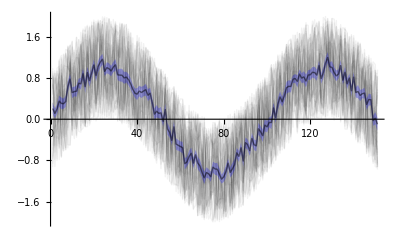

```mathematica
NNListLinePlotMean[ testData,NNErrorPlot->False, NNErrorType->"StandardError" ]
```

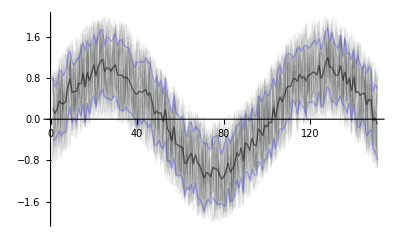

```mathematica
NNListLinePlotMean[ testData,NNErrorPlot->True, NNErrorPlotShaded->False, NNErrorType->"StandardDeviation" ]
```